```mathematica
SetDirectory[NotebookDirectory[]];
<<MappaComplessa2.m
```

```mathematica
?PolarMap
```

```mathematica
?CartesianMap
```

```mathematica
?Picture
?Curves
```

Missing[UnknownSymbol,Picture]

Missing[UnknownSymbol,Curves]

```mathematica
$ContextPath
```

{MappaComplessa2`,System`,Global`}

```mathematica
(* Global` e' il Context di MappaComplessa2, Picture, Curves*)
(* MappaComplessa2` e' il Context di PolarMap, CartesianMap *)
Map[Context, {MappaComplessa2, Picture, Curves, PolarMap, CartesianMap}]
```

{Global`,Global`,Global`,MappaComplessa2`,MappaComplessa2`}

current value of plotpoints= 7

{0.285744,Null}

current value of plotpoints= 7

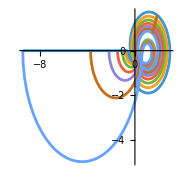
{0.284353,-Graphics-}

```mathematica
(* Altero il valore di PlotPoints *)
SetOptions[Plot, PlotPoints->7];
Timing[CartesianMap[Zeta, {0.1, 0.9}, {0, 20}];]
Timing[CartesianMap[Zeta, {0.1, 0.9}, {0, 20}]]
```

current value of plotpoints= 15

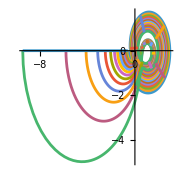
{0.651793,-Graphics-}

```mathematica
SetOptions[Plot, PlotPoints->15];
Timing[CartesianMap[Zeta, {0.1, 0.9}, {0, 20}]]
```

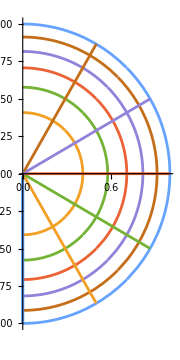
{0.051238,-Graphics-}

```mathematica
SetOptions[Plot, PlotPoints->7];
Timing[PolarMap[Sqrt, {1}, {-Pi+0.0001, Pi}]]
```

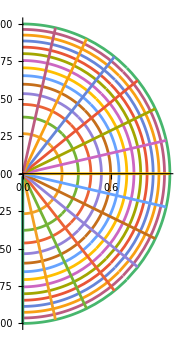
{0.158537,-Graphics-}

```mathematica
SetOptions[Plot, PlotPoints->15];
Timing[PolarMap[Sqrt, {1}, {-Pi+0.0001, Pi}]]
```

```mathematica
SetOptions[Plot, PlotPoints->Automatic];
```

```mathematica
(* Automatic e' Protexted *)
(* Non e' lecito, ad esempio: Automatic=5 *)
```

(DefaultValues[f] restituisce i valori di default delle Options di f)

```mathematica
DefaultValues[Plot];
```

```mathematica
SetOptions[Plot, PlotPoints->15];
DefaultValues[Plot][[1, 2, 50]]
```

PlotPoints→15

```mathematica
SetOptions[Plot, PlotPoints->Automatic];
DefaultValues[Plot][[1, 2, 50]]
```

PlotPoints→Automatic

Possiamo considerare la variante MappaComplessa2MakeLines.m
Essa contiene una riscrittura delle funzioni ausiliarie, compattate in una sola,
lavora in MachinePrecision
usa Line , invece che ParametricPlot (quindi è più veloce, ma più grossolana),
ed ha una conseguente resa in Bianco/Nero dei grafici.

```mathematica
(* Prima, eseguire il Quit del Kernel;
   Quit[] quits only the kernel, not the front end *)
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<MappaComplessa2MakeLines.m
```

```mathematica
(* La funzione ausiliaria sta nel contesto Privato *)
?MakeLines
```

Missing[UnknownSymbol,MakeLines]

```mathematica
(* Global` e' il Context di MappaComplessa2MakeLines, MakeLines *)
(* MappaComplessa2` e' il Context di PolarMap, CartesianMap *)
Map[Context, {MappaComplessa2MakeLines, MakeLines, PolarMap, CartesianMap}]
```

{Global`,Global`,MappaComplessa2MakeLines`,MappaComplessa2MakeLines`}

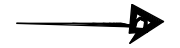
{0.002438,-Graphics-}

```mathematica
SetOptions[Plot, PlotPoints->10];
Timing[CartesianMap[Zeta, {0.1, 0.9}, {0, 20}]]
```

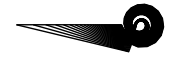
{0.065271,-Graphics-}

```mathematica
SetOptions[Plot, PlotPoints->50];
Timing[CartesianMap[Zeta, {0.1, 0.9}, {0, 20}]]
```

```mathematica
SetOptions[Plot, PlotPoints->50];
Timing[PolarMap[Sqrt, {1}, {-Pi+0.0001, Pi}]]
```

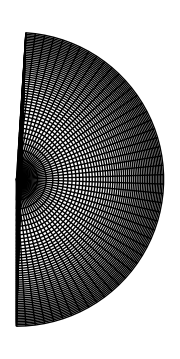
```mathematica
{0.004238,-Graphics-}
```

```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<MappaComplessa3.m
```

```mathematica
(* Lo usage di PolarMap e CartesianMap e' dichiarata tra BeginPackage e BeginPrivate *)
(* MakeLines non ha usage (notare il colore blu); e' ausiliare, nel contesto Private del paccketto MappaComplessa3.m *)
?PolarMap
?CartesianMap
?MakeLines
```

Missing[UnknownSymbol,MakeLines]

```mathematica
(* Grazie a Get, $ContextPath e' stato aggiornato con Context MappaComplessa3` *)
$ContextPath
```

{MappaComplessa3`,ColorDataVisColors`,System`,Global`}

```mathematica
(* I nomi MappaComplessa3, MakeLines sono possibili simboli nel Context Global` (notare il colore blu) *)
(* PolarMap e CartesianMap stanno nel Context MappaComplessa3` *)
Map[Context, {MappaComplessa3, MakeLines, PolarMap, CartesianMap}]
```

{Global`,Global`,MappaComplessa3`,MappaComplessa3`}

```mathematica
SetOptions[Plot, PlotPoints->50];
Timing[CartesianMap[Zeta, {0.1, 0.9}, {0, 20}]]
```

{0.06634,-Graphics-}

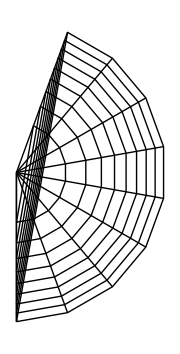
{0.000344,-Graphics-}

```mathematica
SetOptions[Plot, PlotPoints->10];
Timing[PolarMap[Sqrt, {1}, {-Pi+0.0001, Pi}]]
```

Qui sotto, grafichiamo la immagine delle linee che uniscono coordinate in scala logaritmica (inversa della
esponenziale).

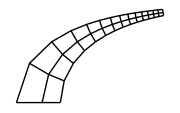
{0.000211,-Graphics-}

```mathematica
(* Chiamata mista *)
SetOptions[Plot, PlotPoints->15];
Timing[CartesianMap[Log, {1, 2, 1/2}, {0, 10}]]
```

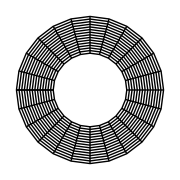

```mathematica
(* Chiamata mista *)
SetOptions[Plot, PlotPoints->15];
PolarMap[Identity, {1, 2}, {-Pi, Pi, Pi/12}]
```

```mathematica
(* numero di Options di Plot, nella versione corrente di Mathematica *)
Length[Options[Plot]]
(* Le plime 7 Options di Plot coi relativi default *)
Options[Plot][[1;;7]]//TableForm
```

65

AlignmentPoint→Center
AspectRatio→1/GoldenRatio
Axes→True
AxesLabel→None
AxesOrigin→Automatic
AxesStyle→{}
Background→None

Nota. In generale ,
- i valori di default sono gli argomenti “posizionali” (di chiamata) di una funzione ,
- mentre le Options sono gli argomenti “nominali” (di chiamata) di una funzione .
Per evitare ambiguità, è meglio mettere tutti i default (posizionali) dopo gli argomenti (di chiamata) obbligatori, se possibile

```mathematica
(* Qui, la funzione g e' definita con 4 argomenti: 2 obbligatori e 2 con default posizionali *)
(* La chiamata di g su due argomenti attiva i valori di default *)
Clear[g];
g[x_, y_:1, z_, t_:2]:={x,y,z,t};
{g[], g[a], g[a, b], g[a, b, c], g[a, b, c, d]}
```

{g[],g[a],{a,1,b,2},{a,b,c,2},{a,b,c,d}}